```mathematica
PerfectDistanceQ[G_]:=(Union@*Flatten@*Round@GraphDistanceMatrix[G] == Range[0,Binomial[VertexCount[G],2]]);

NewWeight[G_]:=
Module[{distances,nextWeight},
distances =DeleteCases[Union@*Flatten@*Round@*GraphDistanceMatrix@*Graph@G,0];nextWeight = Max[AnnotationValue[G,EdgeWeight]]+1;While[(nextWeight<=Length[distances])∧(distances[[nextWeight]]==nextWeight),nextWeight++];
nextWeight
]

(*Computes Children of G in search for Minimal PDGs. Attempting to avoid redundant function calls e.g. computations of GraphDistanceMatrix*)
Children[G_,n_,PDGs_]:=Module[ {vertexCount,edgeCount,vertexList, edgeList, weightList, graphDistanceMatrix,distances,distancesDuplicateFree,newWeight,validNewEdges,GoodChildQ,allChildren,goodChildren},
(*Important values and lists*)
vertexCount=VertexCount[G];
edgeCount = EdgeCount[G];
vertexList = VertexList[G];
edgeList = EdgeList[G];
weightList = AnnotationValue[G,EdgeWeight];
(*GraphDistanceMatrix and associated distances(does not remove duplicates) and distancesDuplicateFree.*)
graphDistanceMatrix = GraphDistanceMatrix[G];
distances= DeleteCases[Flatten@*Round@graphDistanceMatrix,0];
distancesDuplicateFree = Union@distances;
(*Compute newWeight*)
newWeight = Max[weightList]+1;
While[(newWeight<=Length[distancesDuplicateFree])∧(distancesDuplicateFree[[newWeight]]==newWeight),newWeight++];
(*Compute validNewEdges*)
validNewEdges = Join[#1<->#2&@@@Position[UpperTriangularize[graphDistanceMatrix],d_/;newWeight<d],  #<->(vertexCount+1)&/@ vertexList,{(vertexCount+1)<->(vertexCount+2)}];
(*Compute allChildren*)
allChildren = Graph[EdgeAdd[G,#],EdgeWeight->Append[weightList,newWeight]]&/@validNewEdges;
(*Define FastGoodChildQ*)
GoodChildQ[Gchild_]:= (VertexCount[Gchild] <=n) ∧(SubsetQ[Range[Binomial[n,2]],AnnotationValue[Gchild,EdgeWeight]])∧(AllTrue[First/@Select[Tally@DeleteCases[Flatten@GraphDistanceMatrix[Gchild],0.],Last[#]>2&],NewWeight[Gchild]<=#&])∧(Not[AnyTrue[PDGs,IsomorphicSubgraphQ[#,Gchild]&]]);

(* Reducing allChildren to goodChildren*)
goodChildren = DeleteDuplicatesBy[Select[allChildren,GoodChildQ],{LineGraph[#],CanonicalGraph[#]}&];
goodChildren
]
```

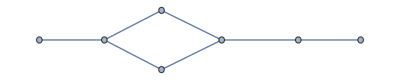
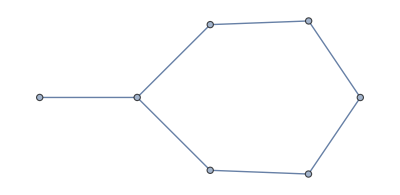
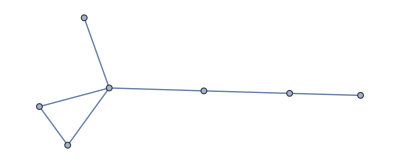
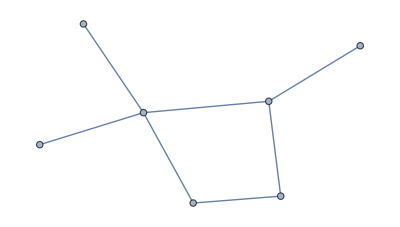
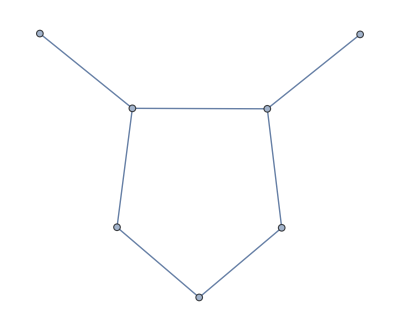
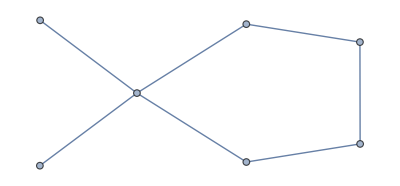
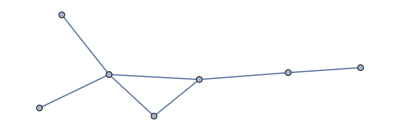
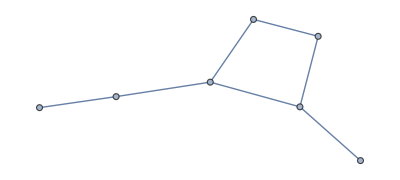
Time To Compute:	00:07:22TimeObject[{0,7,22.2603},Instant] and 260.271ms
Minimal Perfect Distance Graphs(18): 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
n =7;

PDGs = {};
stack =CreateDataStructure["Stack"];
Gstart = Graph[{1<->2},EdgeWeight->{1<->2->1}];

stack["Push",Gstart];

TotalTime = AbsoluteTiming[
(*Depth First Search*)
Until[stack["EmptyQ"],
G = stack["Pop"];
If[(VertexCount[G]==n ∧ PerfectDistanceQ[G]),
PrependTo[PDGs,G];
,(*Else*)
children =Children[G,n,PDGs];
stack["PushList",children];
]
];

][[1]];

reducedPDGs =SortBy[PDGs,EdgeCount];
Do[reducedPDGs = DeleteDuplicatesBy[reducedPDGs,If[IsomorphicSubgraphQ[G,#],G,#]&],{G,reducedPDGs}];
PDGs=reducedPDGs;

Print[
"Time To Compute:\t",TimeObject[{0,0,TotalTime}]," and ",1000FractionalPart[TotalTime],"ms\n",
"Minimal Perfect Distance Graphs(",Length[PDGs],"): \n",TableForm[PDGs,TableDirections->Row],"\n"
]
```